# Discrete Fourier Transform

The Discret Fourier Transform is 
v_s=1/(√n)∑_(r=1)^n u_r e^(2 π i (r-1) (s-1)/n)
the Zero freqeuncy is v_1
the tranform give same result for (s-1)/n or (n-s+1)/n, n and s must be even.
For samll freqeuncy, we should shift the transform and regard the (n-s+1)/n be 1-(s-1)/n or negative freqeuncy
Resolution = 1/(time-interval)
Amplitude ∝ 1/Δt

```mathematica
(* nagative freqeuncy demostration *)
Manipulate[ListPlot[Table[Cos[2π (r-1) (s-1)/n],{r,1,n}]],{s,1,100,1},{n,50,100}]
```

```mathematica
(* shift array *)
Shift[arr_]:=Table[arr[[Mod[i+Length[arr]/2-1,Length[arr]]+1]],{i,1,Length[arr]}];
```

## Example

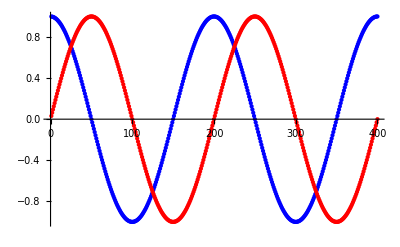

```mathematica
S1=Table[ Cos[2π x],{x,0.005,2,0.005}];
S2=Table[ Sin[2π x],{x,0.005,2,0.005}];
ListPlot[{S1,S2},PlotStyle->{Blue,Red}]
```

```mathematica
(* plot function *)
plot[F_,a_,low_,up_,size_]:=ListPlot[{Re[F],Im[F]},Joined->True,PlotRange->{{Floor[Length[F]/2]+1-a,Floor[Length[F]/2]+1+a},{low,up}},ImageSize->size,Epilog->{Arrow[{{Floor[Length[F]/2]+1,2},{Floor[Length[F]/2]+1,0}}],Arrow[{{Floor[Length[F]/2]-2,2},{Floor[Length[F]/2]+2,2}}]},PlotStyle->{Blue,Red}]
```

```mathematica
Manipulate[Mod[i+Floor[Length[S1]/2-1],Length[S1]]+1,{i,1,Length[S1],1}]
```

```mathematica
FS1=Shift[Fourier[  S1+ ⅈ S2]];
Manipulate[plot[FS1,a,0,20,500],{a,5,30,1}]
```

## NMR Signal

```mathematica
Clear[rawS,refS]
```

```mathematica
rawS[kraw_]:= Cos[kraw 2π x];
refS[k_,ϕ_]:= Cos[k 2π x+ϕ];
```

```mathematica
(* Signal mixing *)
cosS=rawS[kraw] refS[k,0]//TrigReduce
sinS = rawS[kraw] refS[k,π/2]//TrigReduce
```

1/2 (Cos[2 k π x-2 kraw π x]+Cos[2 k π x+2 kraw π x])

1/2 (-Sin[2 k π x-2 kraw π x]-Sin[2 k π x+2 kraw π x])

```mathematica
(* low pass filter *)
1/2 Cos[2 k π x-2 kr π x]
1/2 Sin[2 k π x-2 kr π x]
```

```mathematica
(* form a complex signal *)
comS[kraw_,k_]:=1/2 Cos[2 k π x-2 kraw π x]+ⅈ 1/2 Sin[2 k π x-2 kraw π x]
```

```mathematica
Manipulate[Mod[i+Floor[Length[S]/2-1],Length[S]]+1,{i,1,Length[S],1}]
```

Mod::indet: Indeterminate expression Mod[0, 0] encountered.

```mathematica
maxpos[array_,rank_]:={RankedMax[Re[array],rank],Position[Re[array],RankedMax[Re[array],rank]]}
```

```mathematica
maxpos[FS,1]
```

{10.,{{201}}}

```mathematica
Length[S]
```

400

```mathematica
1/40//N
```

0.025

```mathematica
Manipulate[
{S=Table[comS[f, 12.8],{x,0.05,20,0.05}];
ListPlot[{Re[S],Im[S]},PlotStyle->{Blue,Red}],
FS=Shift[Fourier[ S]];
Manipulate[{plot[FS,a,-10,10,300],plot[Abs[FS],a,0,10,300]},{a,5,30,1}]},{f,12.6,13.0}]
```

```mathematica
Integrate[(1/2 Cos[2 k π x-2 kr π x]+ⅈ 1/2 Sin[2 k π x-2 kr π x])Exp[ⅈ n π/10 x],{x,0,20}]
```

```mathematica
(5 (ⅈ-ⅈ ⅇ^(2 ⅈ n π) Cos[40 (k-kr) π]+ⅇ^(2 ⅈ n π) Sin[40 (k-kr) π]))/((20 k-20 kr+n) π)//ExpToTrig
```

(5 (ⅈ-ⅈ Cos[2 n π] Cos[40 k π-40 kr π]+Cos[40 k π-40 kr π] Sin[2 n π]+Cos[2 n π] Sin[40 k π-40 kr π]+ⅈ Sin[2 n π] Sin[40 k π-40 kr π]))/((20 k-20 kr+n) π)

```mathematica
(5 (Cos[40 k π-40 kr π] Sin[2 n π]+Cos[2 n π] Sin[40 k π-40 kr π]))/((20 k-20 kr+n) π)
(5 (1- Cos[2 n π] Cos[40 k π-40 kr π]+ Sin[2 n π] Sin[40 k π-40 kr π]))/((20 k-20 kr+n) π)
```

```mathematica
Manipulate[Plot[{(5 (Cos[40 k π-40 kr π] Sin[2 n π]+Cos[2 n π] Sin[40 k π-40 kr π]))/((20 k-20 kr+n) π),
(5 (1- Cos[2 n π] Cos[40 k π-40 kr π]+ Sin[2 n π] Sin[40 k π-40 kr π]))/((20 k-20 kr+n) π), √(((5 (Cos[40 k π-40 kr π] Sin[2 n π]+Cos[2 n π] Sin[40 k π-40 kr π]))/((20 k-20 kr+n) π))^2+((5 (1- Cos[2 n π] Cos[40 k π-40 kr π]+ Sin[2 n π] Sin[40 k π-40 kr π]))/((20 k-20 kr+n) π))^2)},{n,-10,10},PlotRange->10],{kr,12.6,13.0},{{k,12.8},12.6,13.0}]
```

```mathematica
Manipulate[ListPlot[{
Table[(5 (Cos[40 k π-40 kr π] Sin[2 n π]+Cos[2 n π] Sin[40 k π-40 kr π]))/((20 k-20 kr+n) π),{n,-10,10}],
Table[(5 (1- Cos[2 n π] Cos[40 k π-40 kr π]+ Sin[2 n π] Sin[40 k π-40 kr π]))/((20 k-20 kr+n) π),{n,-10,10}]},PlotRange->{-7,10},Joined->True],{kr,12.6,13.0},{{k,12.8},12.6,13.0}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.